```mathematica
ratedRpm250=2650;(*rpm*)
ratedTorque250=0.9;(*Nm*)
ratedCurrent250=13.4;(*A*)
v250=24;(*Volts*)
Km250=ratedTorque250/ratedCurrent250;
Kv250=Km250;
noloadCurrent250=1.5;(*A*)'
r250=(v250-Kv250*ratedRpm250*2π/60)/ratedCurrent250;(*ohms*)
frictionTorque250=Km250*noloadCurrent250;

ratedRpm500=2500;(*rpm*)
ratedTorque500=1.9;(*Nm*)
ratedCurrent500=26.7;(*A*)
v500=24;(*Volts*)
noloadCurrent500=2.5;(*A*)
Km500=ratedTorque500/ratedCurrent500;
Kv500=Km500;
r500=(v500-Kv500*ratedRpm500*2π/60)/ratedCurrent500;(*ohms*)
frictionTorque500=Km500*noloadCurrent500;

ratedRpm1000=3000;(*rpm*)
ratedTorque1000=3.18;(*Nm - calculated - 1000/rated ω *)
(*calculated from rated power/rated rpm*)
ratedCurrent1000=35.6;(*A*)
v1000=36;(*Volts*)
Km1000=ratedTorque1000/ratedCurrent1000;
Kv1000=Km1000;
r1000=(v1000-Kv1000*ratedRpm1000*2π/60)/ratedCurrent1000;(*ohms*)

motor500={r-> r500,vRated-> v500,Km-> Km500,Kv-> Kv500,noloadCurrent-> noloadCurrent500,τf-> frictionTorque500}
motor250={r-> r250,vRated-> v250,Km-> Km250,Kv-> Kv250,noloadCurrent-> noloadCurrent250,τf-> frictionTorque250}
motor=motor500;
(*
r=r500;
v= v500;  
Km=Km500;
Kv= Kv500;
noloadCurrent=noloadCurrent500;
τf=frictionTorque500;
*)
ω=rpm/60*2π;
maxrpm=(v-noloadCurrent*r)/Kv*60/2/π;
Print["max rpm = ",maxrpm/.{v-> vRated}/.motor]
```

Null'

{r→0.201127,vRated→24,Km→0.071161,Kv→0.071161,noloadCurrent→2.5,τf→0.177903}

{r→0.400108,vRated→24,Km→0.0671642,Kv→0.0671642,noloadCurrent→1.5,τf→0.100746}

max rpm = 3153.15

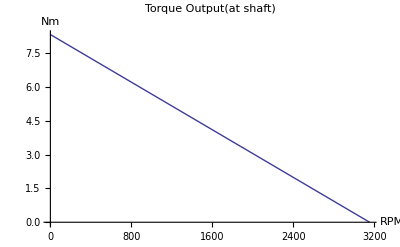

```mathematica
i=(v- Kv*ω)/r;
τg=Km* i;(*torque generated*)
τo=τg-τf;(*torque output*)
Plot[{τo/.{v-> vRated}/.motor},{rpm,0,maxrpm/.{v-> vRated}/.motor},AxesLabel->{"RPM","Nm"},PlotLabel->"Torque Output(at shaft)"]
```

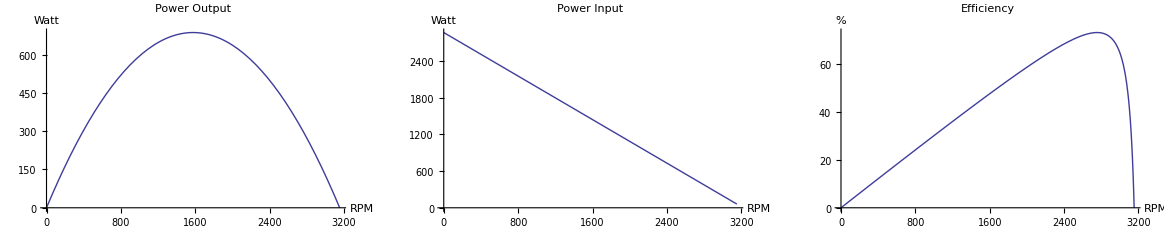

```mathematica
Pout=τo*ω;
τo*maxrpm*2π/60;
Pin=v*i ;
Eff = Simplify[Pout/Pin*100];

(* all the outputs *)
GraphicsRow[{
Plot[Pout/.{v-> vRated}/.motor,{rpm,0,maxrpm/.{v-> vRated}/.motor},AxesLabel->{"RPM","Watt"},PlotLabel->"Power Output"],
Plot[Pin/.{v-> vRated}/.motor,{rpm,0,maxrpm/.{v-> vRated}/.motor},AxesLabel->{"RPM","Watt"},PlotLabel->"Power Input"],
Plot[Eff/.{v-> vRated}/.motor,{rpm,0,maxrpm/.{v-> vRated}/.motor},AxesLabel->{"RPM","%"},PlotLabel->"Efficiency"]
}]
```

ω at max power (ωp) = {165.099}

rmp at max power (ωp) = {1576.58}

max power = {{686.281}}

ω at max efficiency  = 288.446

rmp at max efficiency = 2754.46

max efficiency = {686.281}

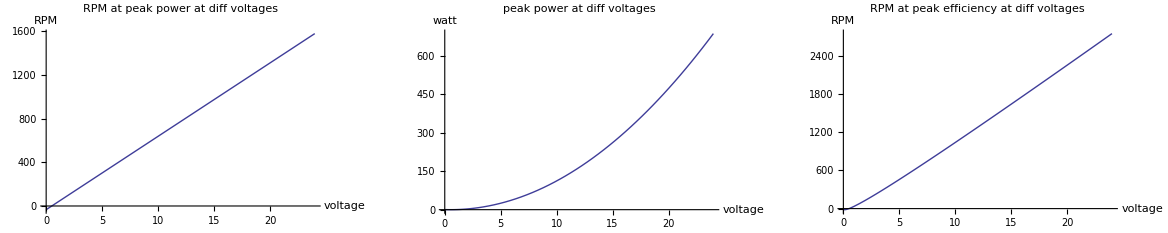

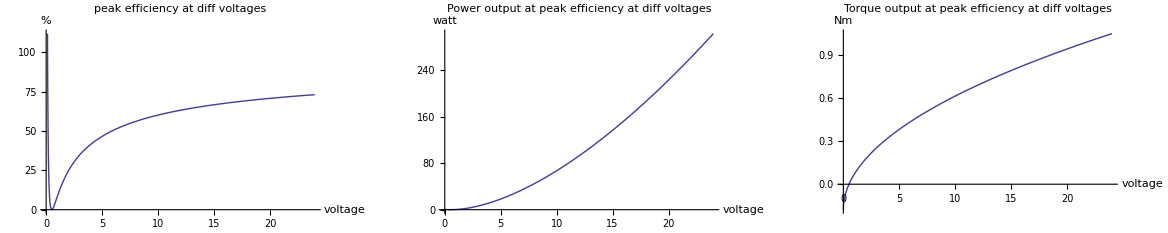

```mathematica
sol1=Solve[D[Pout,rpm]==0,rpm];(*sol1 solves for omega with maximum power output*)
(ω/.sol1)/maxrpm;(*peak torque occurs at half of no load rpm*)
Poutpeak=N[Simplify[Pout/.sol1]];
Print["ω at max power (ωp) = ",ω/.sol1/.{v-> vRated}/.motor];
Print["rmp at max power (ωp) = ",ω*60/2/π/.sol1/.{v-> vRated}/.motor];
Print["max power = ",Poutpeak/.sol1/.{v-> vRated}/.motor];

sol2=Solve[D[Eff,rpm]==0,rpm];(*sol2 solves for rpm with maximum efficiency*)
rpm/.sol2[[1]];(*rpm at which efficiency is maximum*)
(* the first solution- maxima, is the smaller rpm, the other rpm exceeds no load rpm and that point is a minima. hence second solution is discarded*)
Simplify[Eff/.sol2[[1]]];
Print["ω at max efficiency  = ",ω/.sol2[[1]]/.{v-> vRated}/.motor];
Print["rmp at max efficiency = ",ω*60/2/π/.sol2[[1]]/.{v-> vRated}/.motor];
Print["max efficiency = ",Poutpeak/.sol2[[1]]/.{v-> vRated}/.motor];

GraphicsRow[{
Plot[rpm/.sol1/.motor,{v,0,24},AxesLabel->{"voltage","RPM"},PlotLabel->"RPM at peak power at diff voltages"],
Plot[Pout/.sol1/.motor,{v,0,24},AxesLabel->{"voltage","watt"},PlotLabel->"peak power at diff voltages"],
Plot[rpm/.sol2[[1]]/.motor,{v,0,24},AxesLabel->{"voltage","RPM"},PlotLabel->"RPM at peak efficiency at diff voltages"]
}]
GraphicsRow[{
Plot[Eff/.sol2[[1]]/.motor,{v,0,24},AxesLabel->{"voltage","%"},PlotLabel->"peak efficiency at diff voltages"],
Plot[Pout/.sol2[[1]]/.motor,{v,0,24},AxesLabel->{"voltage","watt"},PlotLabel->"Power output at peak efficiency at diff voltages"],
Plot[τo/.sol2[[1]]/.motor,{v,0,24},AxesLabel->{"voltage","Nm"},PlotLabel->"Torque output at peak efficiency at diff voltages"]
}]
```

```mathematica
τo/.{v-> vRated}/.{rpm-> 2500}/.motor
```

1.7221

```mathematica
(*All the parameters that matter*)
Print["maximum no load rpm(maxrpm) = ",maxrpm," = ",maxrpm/.sol1/.{v-> vRated}/.motor];
Print["Current = ",i," = ",i/.{v-> vRated}/.motor];
Print["Torque generated(τg) = ",τg," = ",τg/.{v-> vRated}/.motor];
Print["Torque at the shaft(τo) = ",τo," = ",τo/.{v-> vRated}/.motor];
Print["Torque at the shaft(τo) = ",τo," = ",τo/.{v-> vRated}/.motor];
Print["Power output (Pout)= ",Pout," = ",Pout/.{v-> vRated}/.motor];
Print["Power output peak (Poutpeak) = ",Poutpeak," = ",Poutpeak/.{v-> vRated}/.motor];
Print["ω at which putput power peaks = ",rpm/.sol1," = ",rpm/.sol1/.{v-> vRated}/.motor];
Print["Power Input (Pin) = ",Pin," = ",Pin/.{v-> vRated}/.motor];
Print["Efficiency (Eff)= ",Eff," = ",Eff/.{v-> vRated}/.motor];
```

maximum no load rpm(maxrpm) = (30 (-noloadCurrent r+v))/(Kv π) = {3153.15}

Current = (-1/30 Kv π rpm+v)/r = 4.97199 (24-0.00745197 rpm)

Torque generated(τg) = (Km (-1/30 Kv π rpm+v))/r = 0.353812 (24-0.00745197 rpm)

Torque at the shaft(τo) = (Km (-1/30 Kv π rpm+v))/r-τf = -0.177903+0.353812 (24-0.00745197 rpm)

Torque at the shaft(τo) = (Km (-1/30 Kv π rpm+v))/r-τf = -0.177903+0.353812 (24-0.00745197 rpm)

Power output (Pout)= 1/30 π rpm ((Km (-1/30 Kv π rpm+v))/r-τf) = 1/30 π (-0.177903+0.353812 (24-0.00745197 rpm)) rpm

Power output peak (Poutpeak) = {(0.25 (Km v-1. r τf)^2)/(Km Kv r)} = {686.281}

ω at which putput power peaks = {(15 (Km v-r τf))/(Km Kv π)} = {1576.58}

Power Input (Pin) = (v (-1/30 Kv π rpm+v))/r = 119.328 (24-0.00745197 rpm)

Efficiency (Eff)= (10 π rpm (Km Kv π rpm-30 Km v+30 r τf))/(3 (Kv π rpm-30 v) v) = (5 π (-50.1625+0.0159087 rpm) rpm)/(36 (-720+0.223559 rpm))

```mathematica
(*for 500 watt motor*)
eq1=2.5*R+KV*3150/60*2*π-24;
eq2=26.7*R+KV*2500/60*2*π-24;
Solve[eq1==0&&eq2==0,{R,KV}]
```

{{R→0.200372,KV→0.071238}}

```mathematica
(* from motor calc *)
gear=3;
vel=wrpm*π*d/60;
wrpm=rpm/gear;
τreq2=τreq/gear/.param (*τreq2 is the torque required at the motor *)
motorno=1;
τo/.v-> vRated/.motor
(*
τo=τo*gear/.{v-> vRated}/.motor/.{wrpm-> 800}
*)
(*rpm=wrpm*gear;
*)
```

0.0423333 (42.336+4.43601×10^-7 rpm^2)

-0.177903+0.353812 (24-0.00745197 rpm)

ReplaceAll::reps: {critrpm} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

The maximum rpm achievable for this gear ratio = rpm/.critrpm

47.0799

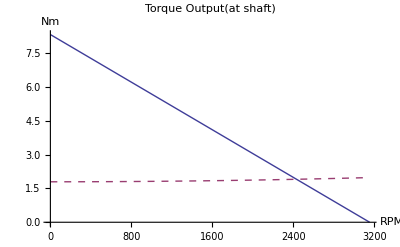

```mathematica
(*critrpm=Solve[(τo*motorno/.motor)==( τreq2/.param),rpm][[2]]*)(*the second one is the positive one .. *)Print["The maximum rpm achievable for this gear ratio = ",rpm/.critrpm/.param/.{v-> vRated}/.motor]
maxvel=wrpm*π*d/60*3600/1000/.param/.{rpm-> 2950}
Plot[{τo*motorno/.{v-> vRated}/.motor,τreq2/.param},{rpm,0,maxrpm/.{v-> vRated}/.motor},AxesLabel->{"RPM","Nm"},PlotLabel->"Torque Output(at shaft)",PlotStyle->{Thick,Dashed}]
```

```mathematica
τreq/.param
```

0.127 (42.336+4.43601×10^-7 rpm^2)